```mathematica
r=2;
vl=4;
vd=2;
dl[ϕ_]:=ϕ*r;(*Bord*)
dd[ϕ_]:=Abs[r] √(2+2Cos[2*ϕ]);(*ligne droit*)
tempsTot[ϕ_]:=(2*dl[ϕ])/vl+dd[ϕ]/vd
```

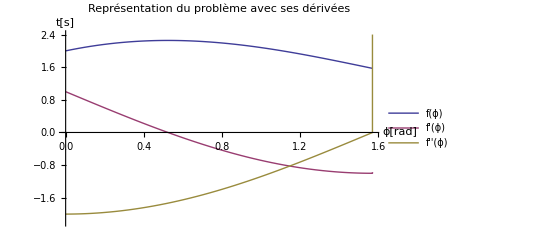

```mathematica
Plot[{tempsTot[ϕ],tempsTot'[ϕ],tempsTot''[ϕ]},{ϕ,0,π/2},PlotRange->{{0,π/2},{-r-r/10,r+r/5}},PlotLegends->{"f(ϕ)","f'(ϕ)","f''(ϕ)"},AxesStyle->Arrowheads[0.02],AxesLabel->{"ϕ[rad]","t[s]"},PlotLabel->"Représentation du problème avec ses dérivées"]
```

```mathematica
Solve[tempsTot'[ϕ]==0,ϕ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ→π/6}}

```mathematica
tempsTot''[π/6]
```

-√3